```mathematica
(*Ecuacion para u'*)
f1[u_,v_]:=(u(1+v)^2)/((1+u v)(u+v))
```

```mathematica
FullSimplify[D[f1[u,v],u]]
FullSimplify[D[f1[u,v],v]]
```

-((-1+u^2) v (1+v)^2)/((u+v)^2 (1+u v)^2)

((-1+u)^2 u (-1+v^2))/((u+v)^2 (1+u v)^2)

```mathematica
(*Ecuacion para v'*)
f2[u_,v_]:=(v(u+v))/(1+u v)
```

```mathematica
FullSimplify[D[f2[u,v],u]]
FullSimplify[D[f2[u,v],v]]
```

(v-v^3)/(1+u v)^2

(u+2 v+u v^2)/(1+u v)^2

```mathematica
D[f1[u,v],u]/.{u->0,v->0}
D[f1[u,v],v]/.{u->0,v->0}
D[f2[u,v],u]/.{u->0,v->0}
D[f2[u,v],v]/.{u->0,v->0}
```

Indeterminate

Indeterminate

0

0

```mathematica
FullSimplify[D[f1[u,v],u]/.{u->1}]
FullSimplify[D[f1[u,v],v]/.{u->1}]
FullSimplify[D[f2[u,v],u]/.{u->1}]
FullSimplify[D[f2[u,v],v]/.{u->1}]
```

0

0

-((-1+v) v)/(1+v)

1

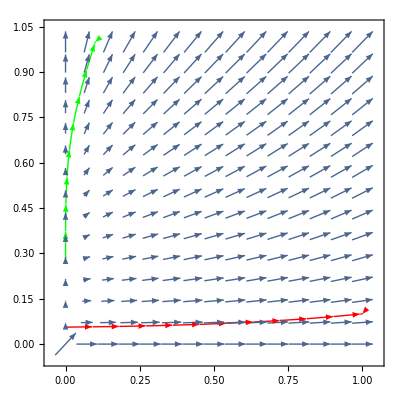

```mathematica
VectorPlot[{f1[u,v],f2[u,v]},{u,0,1},{v,0,1},
StreamPoints->{{{{1,0.1},Red},{{0.1,1},Green}}}]
```

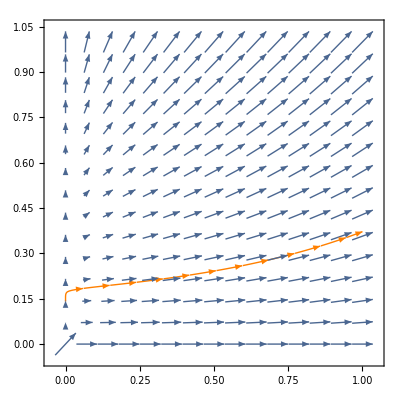

```mathematica
VectorPlot[{f1[u,v],f2[u,v]},{u,0,1},{v,0,1},StreamPoints->{{{{0.2,0.2},Orange}}}]
```